## 非线性方程求解

### 二分法

```mathematica
dichotomy[f_,interval_,eps_]:=FixedPoint[
  With[{a=Min[#],b=Max[#],c=Mean[#]},
   Which[
    f[a]f[c]<0,{a,c},
    f[c]f[b]<0,{c,b},
    (*既不在左半区间，也不在右半区间，直接抛出中点*)
    True,Throw[{c}]
   ]
  ]&,interval,
  SameTest->(Abs[#⟦1⟧-#⟦2⟧]<eps&)
 ]//Catch//Mean
```

```mathematica
dichotomy[x↦Sin[x]-x^2/2,{1.,2.},0.5*^-5]
```

1.40441

### 牛顿法/改进的牛顿法

```mathematica
newton[f_,x0_,r_:1,maxIter_:1000]:=With[
  (*符号计算并化简牛顿法迭代函数*)
  {φ=x↦Evaluate@FullSimplify[x-r f[x]/f'[x]]},
  FixedPoint[φ,x0,maxIter,SameTest->Equal]
 ]
```

```mathematica
newton[x↦x ⅇ^x-1,0.5]
```

0.567143

```mathematica
newton[x↦x^3-x-1,1.]
```

1.32472

```mathematica
newton[x↦(x-1)^2(2x-1),0.45]
```

0.5

```mathematica
newton[x↦(x-1)^2(2x-1),0.65]
```

0.5

```mathematica
newton[x↦(x-1)^2(2x-1),0.55,2,1*^6]
```

0.500177

```mathematica
newtonMonitored[f_,x0_,r_:1,maxIter_:1000,monitor_:None]:=With[
  {φ=x↦Evaluate@FullSimplify[x-r f[x]/f'[x]]},
  FixedPoint[(monitor[#];φ[#])&,x0,maxIter,SameTest->Equal]
 ]
```

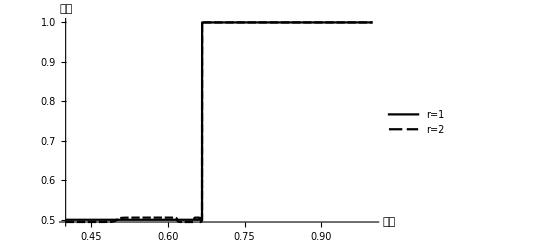

```mathematica
Plot[{newton[x↦(x-1)^2(2x-1),x0,1],newton[x↦(x-1)^2(2x-1),x0,2]},{x0,0.4,1},AxesLabel->{"初值","终值"},PlotLegends->{"r=1","r=2"},PlotTheme->"Monochrome"]
```

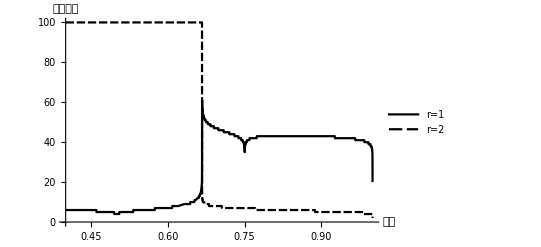

```mathematica
Plot[{Block[{step=0},newtonMonitored[x↦(x-1)^2(2x-1),x0,1,100,step++&];step],
Block[{step=0},newtonMonitored[x↦(x-1)^2(2x-1),x0,2,100,step++&];step]},
{x0,0.4,1},AxesLabel->{"初值","迭代次数"},PlotLegends->{"r=1","r=2"},PlotTheme->"Monochrome"]
```

### 割线法

```mathematica
secant[f_,{x0_,x1_},maxIter_:1000]:=NestWhile[
  With[{xkk=#⟦1⟧,xk=#⟦2⟧},
   {xk,
    xk-f[xk]/(f[xk]-f[xkk])(xk-xkk)
   }]&,{x0,x1},
  Apply[Unequal],1,
  maxIter
 ]⟦2⟧
```

```mathematica
secant[x↦x ⅇ^x-1,{0.4,0.6}]
```

0.567143

### 拟牛顿法

```mathematica
jacobian[f_, dim_] := With[{vars = Table[Unique["var$$"], dim]},
  Function[Evaluate@vars, Evaluate[D[f@@vars, {vars}]]]
 ]
```

```mathematica
quasiNewton[f_,dim_,x0_,maxIter_:1000]:=
 With[{h0=Inverse@*jacobian[f,dim]@@x0},
  FixedPoint[
   Block[{x=#⟦1⟧,h=#⟦2⟧,fx,xnext,r,y,rhy},
    fx=f@@x;
    xnext=x-h.fx;
    r=xnext-x;y=f@@xnext-fx;
    rhy=r.h.y;
    {xnext,
     h+KroneckerProduct[(r-h.y),(r.h)/rhy]}
    ]&,
   {x0,h0},maxIter,
   SameTest->(#1⟦1⟧==#2⟦1⟧&)
  ]⟦1⟧
 ]
```

```mathematica
quasiNewton[{x,y,z}↦{x y-z^2-1,x y z+y^2-x^2-2,ⅇ^x+z-ⅇ^y-3},3,{1.,1.,1.}]
```

{1.77767,1.42396,1.23747}

## 高斯列主元消去法

### 高斯消去法

```mathematica
eliminate[mat_?MatrixQ] := Module[{a = mat},
  Do[
   (*直接消元*)
   a⟦k+1;;, k;;⟧ -= a⟦k+1;;, {k}⟧.a⟦{k}, k;;⟧/a⟦k, k⟧,
   {k, Min@Dimensions@a - 1}
   ];
  a
 ]
```

### 高斯列主元消去

```mathematica
eliminatePE[mat_?MatrixQ] := Module[{a = mat},
  Do[
   With[
    {r = k-1+First@Ordering[Abs@a⟦k;;, k⟧, 1, GreaterEqual]},(*找主元*)
    a⟦{k,r},All⟧ = a⟦{r,k},All⟧(*交换*)
   ];
   a⟦k+1;;, k;;⟧ -= a⟦k+1;;, {k}⟧.a⟦{k}, k;;⟧/a⟦k, k⟧,
   {k, Min@Dimensions@a - 1}
   ];
  a
  ]
```

### 求解

```mathematica
eliminationSolve[a_?MatrixQ,b_?VectorQ,eliminator_]:=
 With[{aa=eliminator[MapThread[Append,{a,b}]],n=Length[aᵀ]},
  Module[{x=ConstantArray[0,n]},
   Do[(*回带*)
    x⟦k⟧=(aa⟦k,n+1⟧-∑_(j=1+k)^n x⟦j⟧ aa⟦k,j⟧)/aa⟦k,k⟧,
    {k,n,1,-1}
   ];
   x
  ]
 ]
```

```mathematica
eliminationSolve[({{10.^-8, 2, 3}, {-1, 3.712, 4.623}, {-2, 1.072, 5.643}}),{1,2,3},eliminate]
```

{-0.491058,-0.0508861,0.367257}

```mathematica
eliminationSolve[({{10^-8, 2, 3}, {-1, 3.712, 4.623}, {-2, 1.072, 5.643}}),{1,2,3},eliminatePE]
```

{-0.491058,-0.0508861,0.367257}

```mathematica
eliminationSolve[({{4, -2, 4}, {-2, 17, 10}, {-4, 10, 9}}),{10,3,7},eliminate]
```

{11/56,-25/28,13/7}

```mathematica
eliminationSolve[({{4, -2, 4}, {-2, 17, 10}, {-4, 10, 9}}),{10,3,7},eliminatePE]
```

{11/56,-25/28,13/7}

## 龙格现象的产生和克服

### 拉格朗日插值

```mathematica
lagrangianInterpolation[points:{{_,_}..}]:=
 With[{px=points⟦All,1⟧,pfx=points⟦All,2⟧,n=Length@points},
  x↦∑_(i=1)^n pfx⟦i⟧∏_(j=1)^n Piecewise[{{(x-px⟦j⟧)/(px⟦i⟧-px⟦j⟧), i≠j}, {1, True}}]
 ]
```

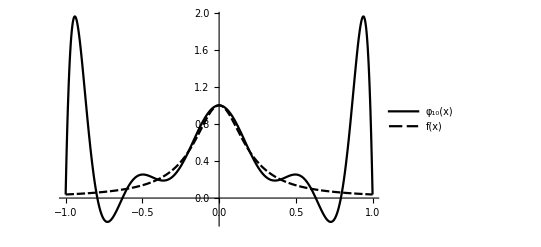

```mathematica
Block[{φ=lagrangianInterpolation[Table[{x,1/(1+25 x^2)},{x,-1,1,1/5}]]},
Plot[{φ[x],1/(1+25 x^2)},{x,-1,1},PlotTheme->"Monochrome",PlotLegends->{Defer[Subscript[φ, 10][x]],Defer[f[x]]}]
]
```

### 分段线性插值

```mathematica
piecewiseLinear[points:{{_,_}..}/;¬OrderedQ[points⟦All,1⟧]]:=
 (*保证输入点按横坐标顺序排列*)
 piecewiseLinear[points//SortBy[First]]
```

```mathematica
piecewiseLinear[points:{{_,_}..}][x_]:=
 With[{px=points⟦All,1⟧,pfx=points⟦All,2⟧,n=Length@points},
  Do[
   If[px⟦i⟧≤x≤px⟦i+1⟧,(*在相邻两插值点间则计算并抛出结果*)
    Throw[(pfx⟦i+1⟧-pfx⟦i⟧)/(px⟦i+1⟧-px⟦i⟧)(x-px⟦i⟧)+pfx⟦i⟧]
   ],
   {i,n-1}];
  Undefined(*插值区间外未定义*)
 ]//Catch
```

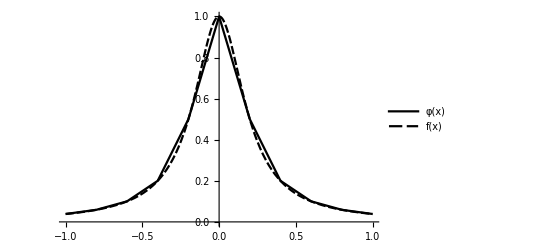

```mathematica
Block[{φ=piecewiseLinear[Table[{x,1/(1+25 x^2)},{x,-1,1,1/5}]]},
Plot[{φ[x],1/(1+25 x^2)},{x,-1,1},PlotTheme->"Monochrome",PlotLegends->{Defer[φ[x]],Defer[f[x]]}]
]
```

### 三次样条插值(三弯矩)

```mathematica
(*差商*)
dq[_,ys_List,0]:=ys
dq[xs_List,ys_List,n_]/;Length[xs]==Length[ys]:=
 Differences[dq[xs,ys,n-1]]/Differences[xs,1,n]
```

```mathematica
(*第一边界条件*)
spline3GetM[1,px_,pfx_,h_,nh_,μ_,λ_,{dfa_,dfb_}]:=
 Module[{cof=SparseArray[{Band[{1,1}]->2,
   Band[{2,1}]->μ,{nh+1,nh}->1,
   Band[{2,3}]->λ,{1,2}->1
  },nh+1],
  d=6dq[px,pfx,2]},
  PrependTo[d,6/h⟦1⟧((pfx⟦2⟧-pfx⟦1⟧)/h⟦1⟧-dfa)];
  AppendTo[d,6/h⟦-1⟧(dfb-(pfx⟦-1⟧-pfx⟦-2⟧)/h⟦-1⟧)];
  LinearSolve[cof,d]
 ]
```

```mathematica
(*第二边界条件*)
spline3GetM[2,px_,pfx_,h_,nh_,μ_,λ_,{d2fa_,d2fb_}]:=
 Module[{cof=SparseArray[{Band[{1,1}]->2,
   Band[{2,1}]->μ⟦2;;⟧,Band[{1,2}]->λ⟦;;-2⟧
  },nh-1],
  d=6dq[px,pfx,2],m},
  d⟦{1,-1}⟧-={μ⟦1⟧d2fa,λ⟦-1⟧d2fb};
  m=LinearSolve[cof,d];
  m~Prepend~d2fa~Append~d2fb
 ]
```

```mathematica
(*计算插值参数*)
spline3GetParams[pts_,type_,boundary_]:=
 Module[{px=pts⟦All,1⟧,pfx=pts⟦All,2⟧,
  h,nh,λ,μ,m,a,b},
  h=Differences[px];nh=Length[h];
  λ=Table[h⟦i+1⟧/(h⟦i⟧+h⟦i+1⟧),{i,nh-1}];
  μ=1-λ;
  m=spline3GetM[type,px,pfx,h,nh,μ,λ,boundary];
  b=pfx⟦;;-2⟧-h^2/6 m⟦;;-2⟧;
  a=Table[(pfx⟦i+1⟧-pfx⟦i⟧)/h⟦i⟧-h⟦i⟧/6(m⟦i+1⟧-m⟦i⟧),{i,nh}];
  {px,pfx,h,m,a,b}
 ]
```

```mathematica
spline3[points:{{_,_}..},type:1|2,boundary:{_,_}:{0,0}]:=
 With[{n=Length[points],
 params=spline3GetParams[SortBy[points,First],type,boundary]},
 With[{px=params⟦1⟧,pfx=params⟦2⟧,h=params⟦3⟧,
 m=params⟦4⟧,a=params⟦5⟧,b=params⟦6⟧},
  x↦Catch[
   Do[
    If[px⟦i⟧≤x≤px⟦i+1⟧,(*在相邻两插值点间则计算并抛出结果*)
     Throw[(px⟦i+1⟧-x)^3/(6h⟦i⟧)m⟦i⟧+(x-px⟦i⟧)^3/(6h⟦i⟧)m⟦i+1⟧+a⟦i⟧(x-px⟦i⟧)+b⟦i⟧]
    ]
    ,{i,n-1}];
   Undefined(*插值区间外未定义*)
  ]
 ]]
```

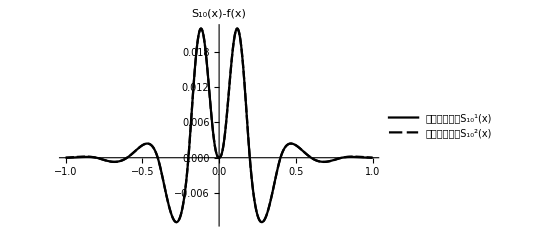

```mathematica
Block[{s1=spline3[Table[{x,1/(1+25 x^2)},{x,-1,1,1/5}],1,D[1/(1+25 x^2),x]/.{x->{-1,1}}],
s2=spline3[Table[{x,1/(1+25 x^2)},{x,-1,1,1/5}],2,D[1/(1+25 x^2),{x,2}]/.{x->{-1,1}}]},
Plot[{s1[x]-1/(1+25 x^2),s2[x]-1/(1+25 x^2)},{x,-1,1},PlotTheme->"Monochrome",PlotLabel->Defer[Subscript[S, 10][x]-f[x]],PlotRange->Full,
PlotLegends->{StringForm["第一边界条件`1`",Defer[(Subscript[S, 10]^1)[x]]],StringForm["第二边界条件`1`",Defer[(Subscript[S, 10]^2)[x]]]}]
]
```

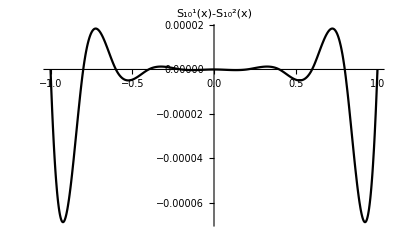

```mathematica
Block[{s1=spline3[Table[{x,1/(1+25 x^2)},{x,-1,1,1/5}],1,D[1/(1+25 x^2),x]/.{x->{-1,1}}],
s2=spline3[Table[{x,1/(1+25 x^2)},{x,-1,1,1/5}],2,D[1/(1+25 x^2),{x,2}]/.{x->{-1,1}}]},
Plot[s1[x]-s2[x],{x,-1,1},PlotTheme->"Monochrome",PlotRange->Full,PlotLabel->Defer[(Subscript[S, 10]^1)[x]-(Subscript[S, 10]^2)[x]]]
]
```

## 龙贝格积分法

```mathematica
romberg[f_,{a_,b_},monitor_:None]:=
 Module[{k=1,h=b-a,n=1,t={(b-a)/2.(f[a]+f[b])}},
  While[
   monitor[t];
   (*梯形法递推*)
   AppendTo[t,t⟦-1⟧/2+h/2∑_(i=0)^(n-1) f[a+h(i+1/2)] ];
   (*外推加速*)
   Do[t⟦k-m+1⟧=(4^m t⟦k-m+2⟧-t⟦k-m+1⟧)/(4^m-1),{m,1,k}];
   h/=2;n*=2;++k;
   t⟦1⟧≠t⟦2⟧
  ];
  monitor[t];
  t⟦1⟧
 ]
```

```mathematica
incompleteTranspose[m_]:=(*辅助函数-不完全数组转置*)
 PadRight[m,{Length[m],Max[Length/@m]},"p"]ᵀ/.{"p"->Nothing}
(*从原始数据构造T-数表*)
makeTTable=incompleteTranspose@*incompleteTranspose;
```

```mathematica
{result,{t}}=romberg[x↦x^3,{6,100},Sow]//Reap;
makeTTable[t]//TableForm
result
```

4.70102×10^7 | 3.05023×10^7 | 2.63753×10^7
2.49997×10^7 | 2.49997×10^7 | 
2.49997×10^7 |  |

2.49997×10^7

```mathematica
{result,{t}}=romberg[x↦Piecewise[{{Sin[x]/x, x≠0}, {1, True}}],{0,1},Sow]//Reap;
makeTTable[t]//TableForm//Style[#,Small]&
result
```

0.920735 | 0.939793 | 0.944514 | 0.945691 | 0.945985 | 0.946059
0.946146 | 0.946087 | 0.946083 | 0.946083 | 0.946083 | 
0.946083 | 0.946083 | 0.946083 | 0.946083 |  | 
0.946083 | 0.946083 | 0.946083 |  |  | 
0.946083 | 0.946083 |  |  |  | 
0.946083 |  |  |  |  |

0.946083

```mathematica
{result,{t}}=romberg[x↦Sin[x^2],{0,1},Sow]//Reap;
makeTTable[t]//TableForm//Style[#,Small]&
result
```

0.420735 | 0.33407 | 0.315975 | 0.31168 | 0.31062 | 0.310356 | 0.31029
0.305181 | 0.309944 | 0.310249 | 0.310267 | 0.310268 | 0.310268 | 
0.310261 | 0.310269 | 0.310268 | 0.310268 | 0.310268 |  | 
0.310269 | 0.310268 | 0.310268 | 0.310268 |  |  | 
0.310268 | 0.310268 | 0.310268 |  |  |  | 
0.310268 | 0.310268 |  |  |  |  | 
0.310268 |  |  |  |  |  |

0.310268